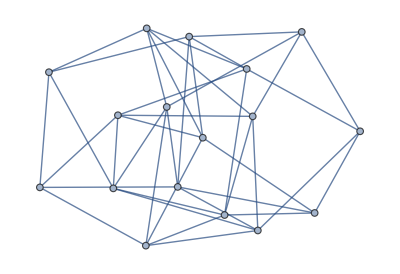
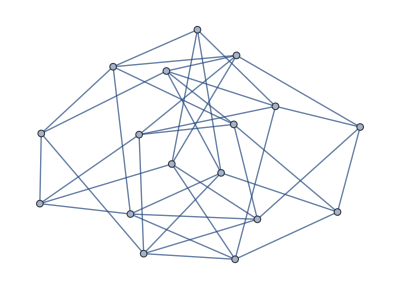
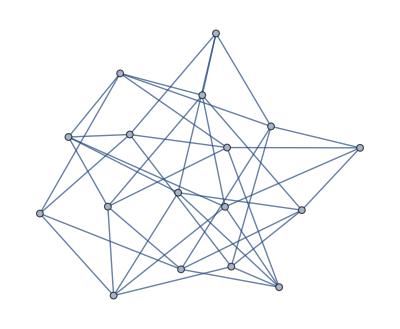
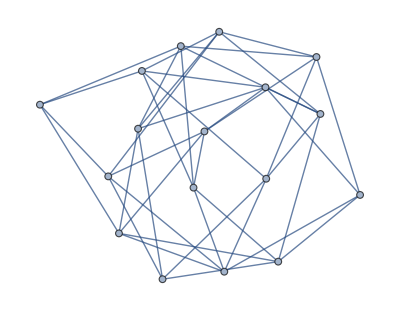
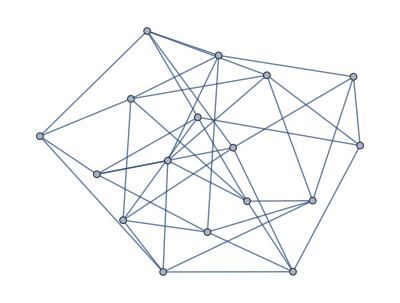
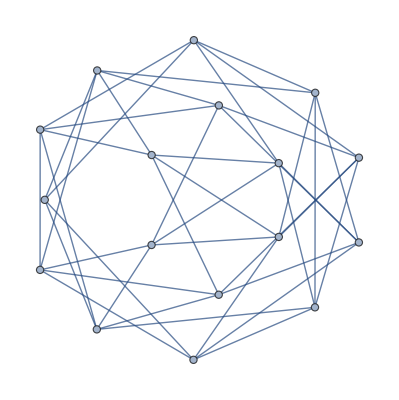
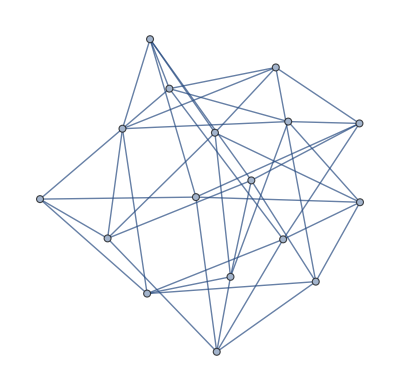

{{4,4,4,4,4,5,5,5,5,5,5,5,5,5,5,5,5},{4,4,4,4,4,5,5,5,5,5,5,5,5,5,5,5,5},{4,4,4,5,5,5,5,5,5,5,5,5,5,5,5,5,5},{4,4,4,5,5,5,5,5,5,5,5,5,5,5,5,5,5},{4,4,4,5,5,5,5,5,5,5,5,5,5,5,5,5,5},{4,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5},{4,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5}}

False

```mathematica
gl=Import["https://a-boy.tk/playmath/stage17-Ramsey-Numbers/r36_17.g6"];
gl={gl[[3]],gl[[5]],gl[[1]],gl[[2]],gl[[4]],gl[[6]],gl[[7]]}
VertexDegree/@gl
IsomorphicGraphQ[gl[[6]],gl[[7]]]
```

```mathematica
HighlightGraph[gl[[7]],FindHamiltonianCycle[gl[[6]],1]];
```

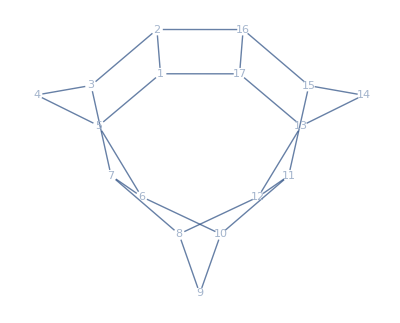
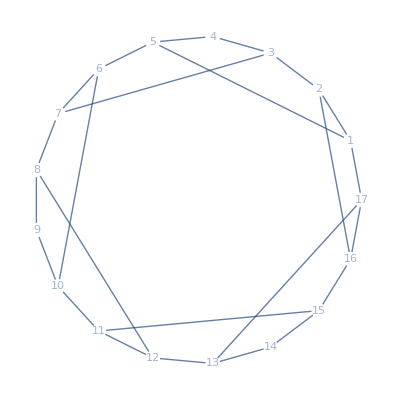

```mathematica
circleLayout[n_]:=Table[{Cos[2π/n i],Sin[2π/n i]},{i,n}];
papaya=AdjacencyGraph[{{0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1},{1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,1,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,1,0,0,1,0,0,0,0,0,0,0},{0,0,1,0,0,1,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,1,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,1,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,1,0,0,1,0,0},{0,0,0,0,0,0,0,1,0,0,1,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,1,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1},{1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0}}];
{GraphPlot[papaya,VertexShapeFunction->"Name"],GraphPlot[papaya,VertexShapeFunction->"Name",VertexCoordinates->circleLayout[17]]}
Table[GraphPlot[papaya,VertexShapeFunction->"Name",GraphLayout->layout],{layout,{"DiscreteSpiralEmbedding","HighDimensionalEmbedding","BalloonEmbedding","LinearEmbedding","StarEmbedding",}}]
```

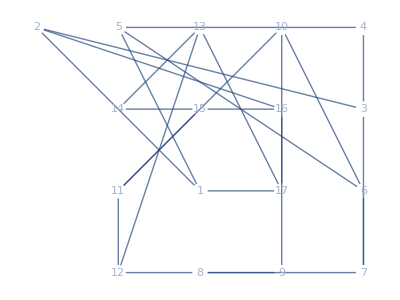
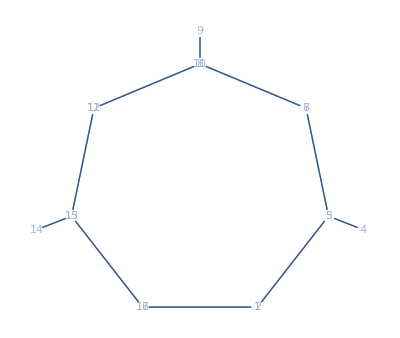
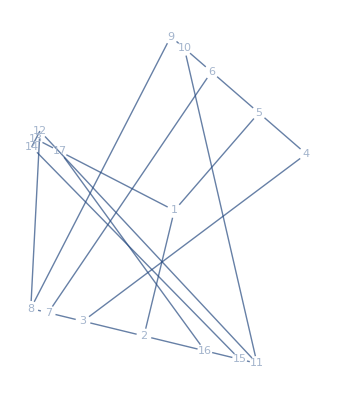
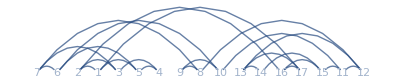
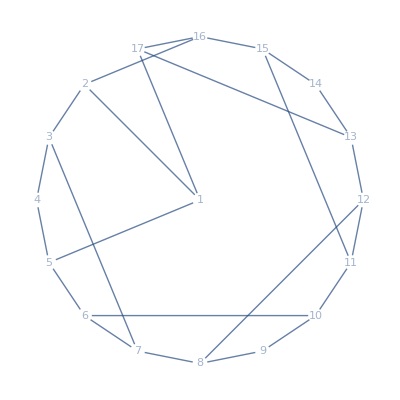
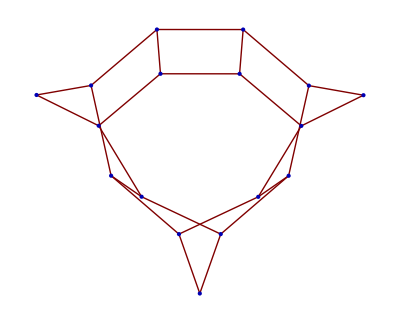

```mathematica
Table[
assoc=FindSubgraphIsomorphism[papaya,gl[[k]],1][[1]];
reverseAssoc=Association@KeyValueMap[#2->#1&,assoc];
g=Graph[EdgeList[gl[[k]]]/.reverseAssoc];
sub=FindIsomorphicSubgraph[g,papaya,1][[1]];
GraphPlot[g,VertexShapeFunction->"Name",GraphLayout->"CircularEmbedding"]+GraphPlot[sub,VertexShapeFunction->"Name"]+
GraphPlot[body=GraphDifference[g,sub],VertexShapeFunction->"Name"],
{k,7}]
```

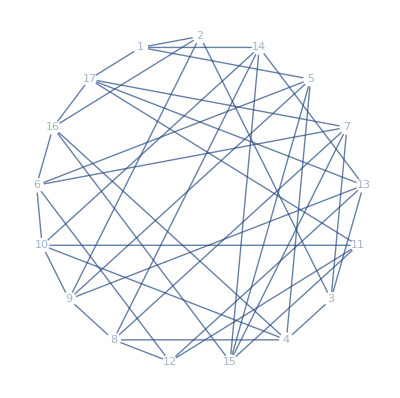
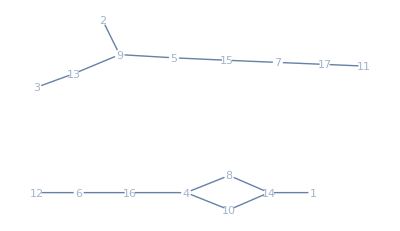
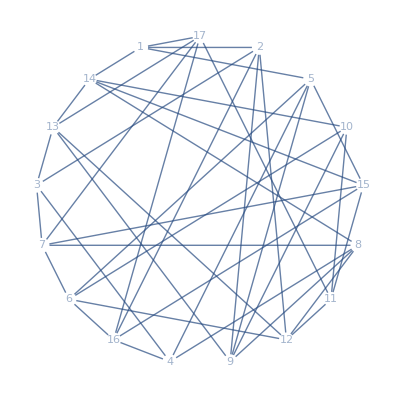
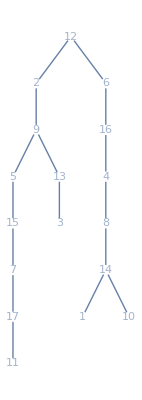
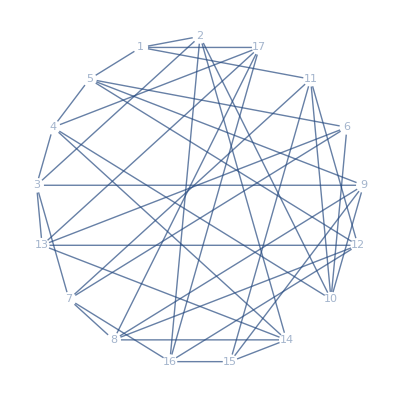
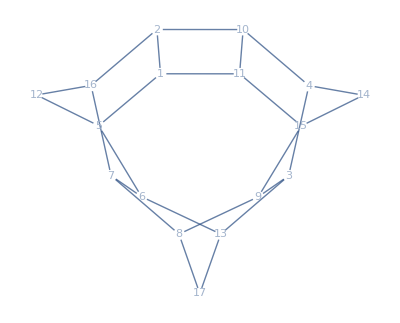
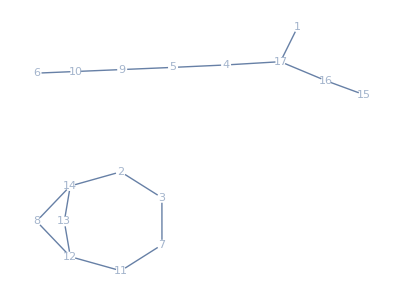
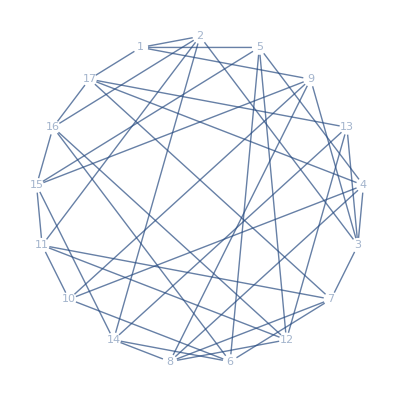
```mathematica
{-Graphics-+-Graphics-+-Graphics-,-Graphics-+-Graphics-+-Graphics-,-Graphics-+-Graphics-+-Graphics-,-Graphics-+-Graphics-+-Graphics-,-Graphics-+-Graphics-+-Graphics-,-Graphics-+-Graphics-+-Graphics-,-Graphics-+-Graphics-+-Graphics-}
```